# Single-atom in cavity LASER

### plotting differences

```mathematica
R1 = (0.13031296482741567-0.3709541882387141)/(0.13031296482741567+0.3709541882387141)
R2 = (0.2609952216847981-0.3582013642373096)/(0.2609952216847981+0.3582013642373096)
R3 = (0.38113366255585135-0.34478844345898874)/(0.38113366255585135+0.34478844345898874)
R5=(0.5692202870525652-0.3178568723106907)/(0.5692202870525652+0.3178568723106907)
R10=(0.7042398796774734-0.20758186360271633)/(0.7042398796774734+0.20758186360271633)
R15=(0.4934259414587624-0.1963713874871449)/(0.4934259414587624+0.1963713874871449)
R20 = (0.20084-0.100764)/(0.20084+0.100764)
```

-0.480066

-0.156988

0.0500677

0.283361

0.544688

0.43064

0.331813

```mathematica
Rdata = {{1,R1}, {2,R2},{3,R3},{5,R5},{10,R10},{15,R15},{20,R20}};
```

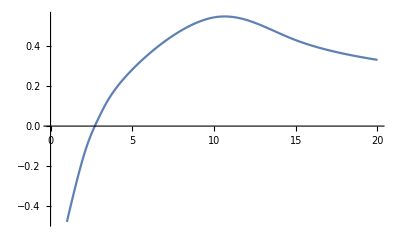

```mathematica
ListLinePlot[Normal@Rdata, InterpolationOrder->3]
```

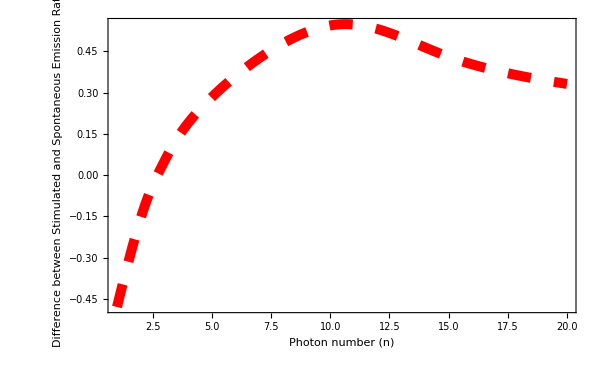
ShowLegend[-Graphics-]

```mathematica
ShowLegend[Show[ListLinePlot[Rdata,InterpolationOrder->3,PlotStyle-> {{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}],Red,Thickness[0.012]]}},Frame->True,FrameLabel->{"Photon number (n)","Difference between Stimulated \n and Spontaneous Emission Rates"},FrameStyle->Directive[Black, AbsoluteThickness[1.2]],BaseStyle->{FontWeight->"Bold",FontSize->18},PlotRange->All,ImageSize->{600,500},PlotLabel->Style["",FontSize->10],PlotRangeClipping->False,ImagePadding->{{Automatic,20},{Automatic,Automatic}},PlotLabel->Style["",FontSize->10]]]]
```

```mathematica
Q1 = -0.7295835436608656
Q2 = -0.7222325324847781
Q3=-0.7265401666307648
Q5=-0.7328231506516797
Q10=-0.6474607090017438
Q15=-6.102513633413125
```

-0.729584

-0.722233

-0.72654

-0.732823

-0.647461

-6.10251

```mathematica
Qdata = {{1,Q1}, {2,Q2},{3,Q3},{5,Q5},{10,Q10},{15,Q15}};
```

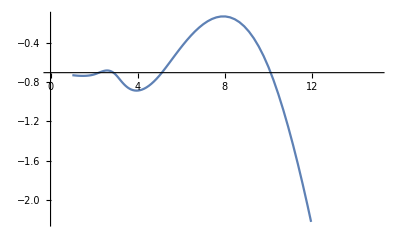

```mathematica
ListLinePlot[Normal@Qdata, InterpolationOrder->3]
```

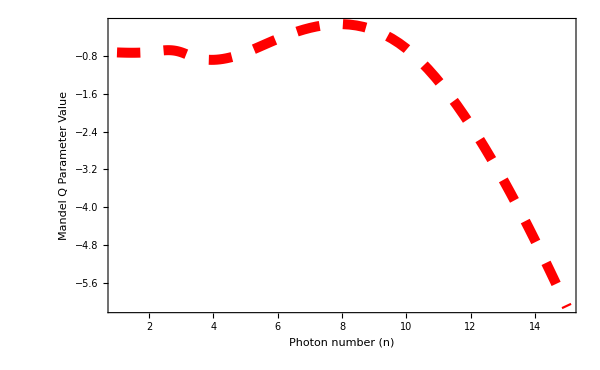
ShowLegend[-Graphics-]

```mathematica
ShowLegend[Show[ListLinePlot[Qdata,InterpolationOrder->3,PlotStyle-> {{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}],Red,Thickness[0.012]]}},Frame->True,FrameLabel->{"Photon number (n)","Mandel Q \n Parameter Value"},FrameStyle->Directive[Black, AbsoluteThickness[1.2]],BaseStyle->{FontWeight->"Bold",FontSize->18},PlotRange->All,ImageSize->{600,500},PlotLabel->Style["",FontSize->10],PlotRangeClipping->False,ImagePadding->{{Automatic,20},{Automatic,Automatic}},PlotLabel->Style["",FontSize->10]]]]
```